```mathematica
f[x_, y_] := Exp[x]*(x+1)+y/(x+1);
a = 0; 
b = 2;
x0=0;
y0=1;
h=0.1;
m = Floor[(b-a)/h]+1;
```

|   x |   y
 |      0 |      1
 |     0.1 |  1.2157
 |     0.2 |  1.4657
 |     0.3 |  1.7548
 |     0.4 |  2.0886
 |     0.5 |  2.4731
 |     0.6 |  2.9154
 |     0.7 |  3.4234
 |     0.8 |   4.006
 |     0.9 |  4.6732
 |      1. |  5.4366
 |     1.1 |  6.3087
 |     1.2 |  7.3043
 |     1.3 |  8.4394
 |     1.4 |  9.7325
 |     1.5 |  11.204
 |     1.6 |  12.878
 |     1.7 |   14.78
 |     1.8 |  16.939
 |     1.9 |  19.389
 |      2. |  22.167

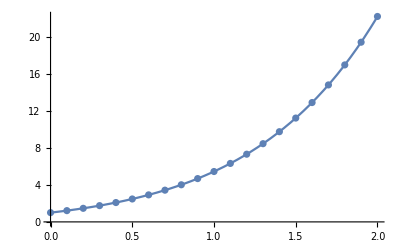

```mathematica
rk4[f_,x0_,y0_,h_,m_]:=Block[{k1,k2,k3,k4,x=x0,y=y0,t,k},
"Вспомогательные функции";
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
"Таблица приближенных значений t = tab1";
t=Table[{x,y}=
{x+h,y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6},
{k,m-1}];
t=Prepend[t,{x0,y0}];
Return[t]]
tab1:=rk4[f,x0,y0,h,m]
gr3:=ListPlot[tab1]
lst={{},{"  x","  y"}};
PaddedForm[TableForm[tab1,TableHeadings->lst],5]
g[x_] :=Exp[x]*(x+1)
gr2:=Plot[g[x],{x,a,b}]
Show[{gr3,gr2}]
```

```mathematica
x=x0;y=y0;
eul=Table[{x,y}={x+h,y+h*f[x,y]},{i,m-1}];
eul=Prepend[eul,{x0,y0}];
gr1:=ListPlot[eul]
```

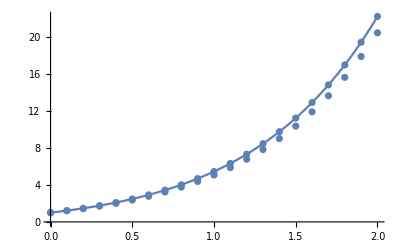

```mathematica
Show[{gr3,gr1,gr2}]
```